## Directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jimak\Desktop\Bachelor thesis\Mathematica files

## Constants

```mathematica
obh2pl=0.02236;
(*the Ωbh^2 value from the Planck paper https://arxiv.org/pdf/1807.06209.pdf*)
ompl=0.3166;
(*the Ωm value from Planck*)
H0pl=67.27;
(*the H0 value from planck*)
h0pl=Hopl/100;

h0riess=0.7403;
(*the h value from SN1a https://arxiv.org/pdf/1903.07603.pdf *)
Tcmb=2.7255;
(*the CMB temperature*)
c=299792.458; (*the speed of light in km/s*)
cHo=2997.92458;
```

## X^2 analysis

```mathematica
(*transition model*)f1[a_,w0_,wa_,n_]:=(a^(-3*(1+w0+wa)))*(E^(-3*wa*HarmonicNumber[n]+3*a*n*wa*HypergeometricPFQ[{1,1,1-n},{2,2},a]))
```

```mathematica
zeq[om_?NumberQ,h_?NumberQ]:=2.5*(10^4)*om*(h^2)*((Tcmb/2.7)^(-4))
```

```mathematica
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h])
```

```mathematica
(*dimensionless Hubble parameter*)
```

```mathematica
e[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=Sqrt[a^(-3)*om*(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))f1[a,w0,wa,n]]
```

```mathematica
(*Sound speed*)
cs[a_?NumberQ,obh2_?NumberQ]:=c/(Sqrt[3(1+(31500 obh2(Tcmb/2.7)^-4)a)] )
```

```mathematica
(*redshift at decupling A. Theodoropoulos page 37, eq 2.42*)
g1[obh2_?NumberQ]:=(0.0783*(obh2)^(-0.238))/(1+39.5*(obh2)^(0.763));
g2[obh2_?NumberQ]:=0.560/(1+21.1*(obh2)^(1.81));
zdec[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1048(1+0.00124(obh2)^(-0.738))*(1+g1[obh2]*(om*(h^2))^(g2[obh2]));

(*comoving sound horizon*)
rs[ze_,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=NIntegrate[cs[x,obh2]/((x^2)*100h*e[x,om,w0,wa,n,h]),{x,0,1/(1+ze)}]
```

```mathematica
rs[1100,0.31,0.0224,-1,0,1,0.674]
```

144.208

```mathematica
(*comoving sound horizon at decoupling*)
rsdec[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=NIntegrate[cs[a,obh2]/((a^2)*100h*e[a,om,w0,wa,n,h]),{a,0,1/(1+zdec[om,obh2,h])}]
```

```mathematica
hz[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=100h*e[1/(1+z),om,w0,wa,n,h]
```

```mathematica
(*luminosity distance*)
```

```mathematica
Clear[DLsol,DL,dL]
DLsol[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(DLsol[om,w0,wa,n,h]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(h*100*e[1/(1+zz),om,w0,wa,n,h]/(100h)),dL[0]==0},dL,{zz,0,1300},MaxSteps->Infinity])
DL[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=((c/(100h))dL[z]/.DLsol[om,w0,wa,n,h])[[1]]//Chop
```

```mathematica
(*angular diameter distance*)
DA[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=DL[z,om,w0,wa,n,h]/(1+z)^2
```

```mathematica
(*comoving angular distance at decoupling*)
Dm1[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(c/(100*h))*NIntegrate[(hz[z,om,w0,wa,n,h]/100h)^(-1),{z,0,zdec[om,obh2,h]}];
Dm2[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(zdec[om,obh2,h]+1)*DA[zdec[om,obh2,h],om,w0,wa,n,h];
Dm3[z_?NumberQ,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(z+1)*DA[z,om,w0,wa,n,h]
```

```mathematica
Dv[z_,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=((c*z*((1+z)^2)*(DA[z,om,w0,wa,n,h]^2))/hz[z,om,w0,wa,n,h])^(1/3)
```

```mathematica
(*BAO dz ratio =rs/Dv*)
dz[z_,om_,obh2_,w0_,wa_,n_,h_]:=rs[zdec[om,obh2,h],om,obh2,w0,wa,n,h]/Dv[z,om,w0,wa,n,h]
```

```mathematica
DH[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=c/hz[z,om,w0,wa,n,h]
```

```mathematica
(*CMB shift parameter*)
R[om_,obh2_,w0_,wa_,n_,h_]:=(Sqrt[om (100h)^2]*Dm2[om,obh2,w0,wa,n,h])/c
```

```mathematica
(* Drag redshift: https://arxiv.org/pdf/astro-ph/9709112.pdf eq 4 page 5*)
zdrag[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1291 ((om*h^2)^0.251)/(1+0.659 (om*h^2)^0.828)(1+(0.313(om*h^2)^-0.419(1+0.607(om*h^2)^0.674))(obh2)^(0.238(om*h^2)^0.223))
```

```mathematica
la[om_,obh2_,w0_,wa_,n_,h_]:=(Pi*Dm2[om,obh2,w0,wa,n,h])/rsdec[om,obh2,w0,wa,n,h]
```

```mathematica
(*dx*)
dX[nsig_,M_]:=2*InverseGammaRegularized[M/2,1-Erf[nsig/(Sqrt[2])]]//N;
```

## New BAO data

```mathematica
baodata={(*{0.38,10.27,0.15},*){0.51,13.38,0.18},(*{0.7,17.48,0.23},*)(*{0.7,17.65,0.3},*){0.7,17.96,0.51},{0.77,18.85,0.38},(*{0.835,18.92,0.51},*){0.85,19.51,0.41}(*,{0.845,18.90,0.78}*)(*,{0.845,19.84,0.53}*),{0.85,19.5,1},{1.48,30.21,0.79},{2.33,37.5,1.1},(*{0.11,1.95,0.10},*){0.7,17.28,0.89},{0.87,21.39,1.39},{1.00,23.13,2.07},{2.00,36.18,1.69},{2.35,36.3,1.8},{2.40,36.6,1.2},{2.34,37.72,2.18},(*{2.36,36.29,1.34},*){0.38,10.27,0.15},(*{0.51,13.38,0.18},*){0.61,15.45,0.22},{0.81,19.46,0.78},(*{2.40,36.6,1.2},*){0.32,8.76,0.14},{0.44,11.79,1.11},(*{0.51,11.92,0.18},*){0.54,14.76,0.68},{0.6,14.99,1.04},{0.73,18.03,1.26}(*,{2.34,37.68,2.17},{2.36,36.29,1.34}*),{0.51,13.62,0.25},{0.71,16.85,0.32},{0.93,21.71,0.28},{1.32,27.79,0.69},{2.33,39.71,0.94},{0.59,15.29,0.25},{0.32,8.54,0.25},{0.8,19.54,2.07},{1.5,30.51,1.85},{2.2,38.09,1.73}}; 
Length[baodata]
```

32

```mathematica
X2bao4[om_?NumberQ,obh2_?NumberQ,w0_,wa_,n_,h_?NumberQ]:=Sum[(baodata[[i,2]]-(Dm3[baodata[[i,1]],om,obh2,w0,wa,n,h]/147.18(*rd*)))^2/(baodata[[i,3]]^2+(0.29(*rd σ*))^2),{i,1,Length[baodata]}]
```

```mathematica
minBao=FindMinimum[X2bao4[om,obh2pl,-1,0,1,h],{om,0.28},{h,0.65}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{17.7064,{om→0.342809,h→0.674518}}

```mathematica
omBaonew=minBao[[2,1,2]];
hBaonew=minBao[[2,2,2]];
```

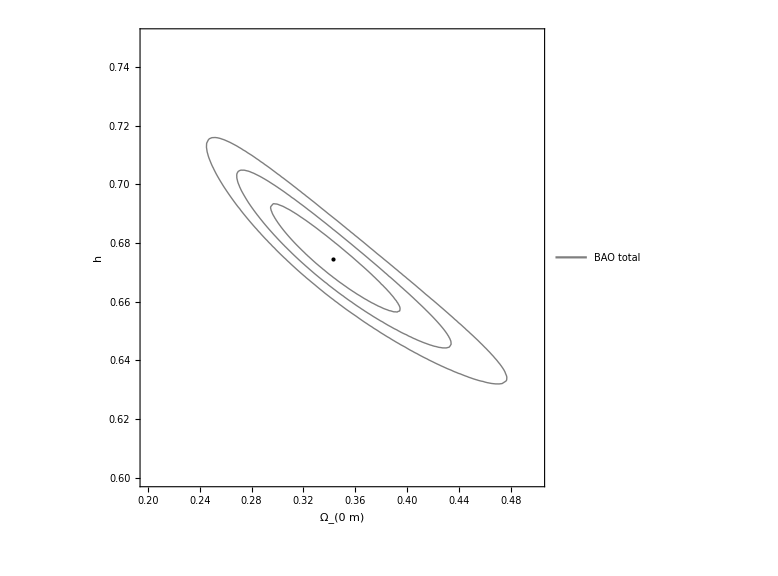

```mathematica
contourBAOnew =ContourPlot[X2bao4[om,obh2pl,-1,0,1,h],{om,0.2,0.5},{h,0.6,0.75},Contours->{minBao[[1]]+dX[1,2],minBao[[1]]+dX[2,2],minBao[[1]]+dX[3,2]},FrameLabel->{"Ω_(0  m)","h"},BaseStyle->{FontFamily->"Times",25},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{omBaonew,hBaonew}]}},ContourShading->False,ContourStyle->Thick,ImageSize->Large, WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"BAO total"},{0.7,0.7}]]
```

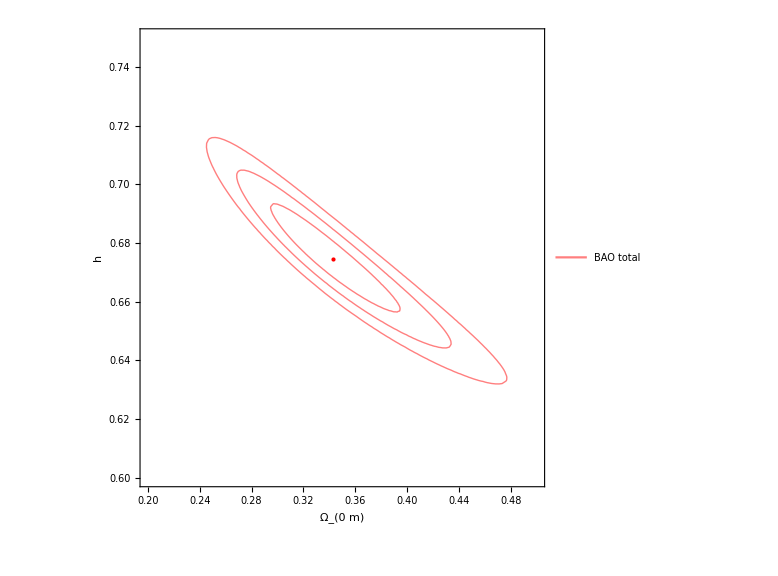

```mathematica
contourBAOnewred=ContourPlot[X2bao4[om,obh2pl,-1,0,1,h],{om,0.2,0.5},{h,0.6,0.75},Contours->{minBao[[1]]+dX[1,2],minBao[[1]]+dX[2,2],minBao[[1]]+dX[3,2]},FrameLabel->{"Ω_(0  m)","h"},BaseStyle->{FontFamily->"Times",25},FrameStyle->Directive[Black],ContourStyle->Red,Epilog->{{PointSize[Large],Red,Point[{omBaonew,hBaonew}]}},ContourShading->False,ContourStyle->Thick,ImageSize->Large, WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"BAO total"},{0.7,0.6}]]
```

## Errors for the bao data

```mathematica
chifunBaonew=ListInterpolation[ParallelTable[X2bao4[om,obh2pl,-1,0,1,h],{om,omBaonew-0.02,omBaonew+0.02,0.02},{h,hBaonew-0.002,hBaonew+0.002,0.002},DistributedContexts->Automatic],{{omBaonew-0.02,omBaonew+0.02},{hBaonew-0.002,hBaonew+0.002}}];
```

```mathematica
paramsBao={om,h};
```

```mathematica
FijBaonew=0.5*Table[D[chifunBaonew[om,h],paramsBao[[p]],paramsBao[[d]]]/.minBao[[2]],{p,1,Length[paramsBao]},{d,1,Length[paramsBao]}];
cijBaonew=Inverse[FijBaonew];
```

```mathematica
errorsBaonew=Sqrt[Diagonal[cijBaonew]]
```

{0.03318,0.0122481}

```mathematica
Print["The best fit parameters for Ω_(0  m) and h (newer sample) are:"," Ω_(0  m)=",NumberForm[omBAOnew,3]," ± ",NumberForm[errorsBaonew[[1]],1]," and h=",NumberForm[hBAOnew,3]," ± ",NumberForm[errorsBaonew[[2]],1]," respectively."]
```

The best fit parameters for Ω_(0  m) and h (newer sample) are: Ω_(0  m)=omBAOnew ± 0.03 and h=hBAOnew ± 0.01 respectively.

## Pantheon+ data

```mathematica
(*the full data can be found at https://github.com/PantheonPlusSH0ES/DataRelease/tree/main/Pantheon%2B_Data/4_DISTANCES_AND_COVAR and was used in https://arxiv.org/abs/2301.01024*)
dataP=Import[".\\data\\Pantheon+SH0ES.txt","Table"];
(*length of the Pantheon+ data*)
ndatP=Length[dataP]-1;
(*statistical and systematic errors*)
Dij0=Import[".\\data\\Pantheon+SH0ES_STAT+SYS.cov","List"];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
(*Partition: Takes the elements from the second to the last of list Dij0 (thus [[2;;-1]]) and partitions them into sublists, each having a length of 1701 (thus {Dij0[[1]]}=1701)*)
Covstat=DiagonalMatrix[dataP[[All,10]][[2;;-1]]^2];
Covtot=Dij;
InvCovtot=Inverse[Covtot]
```

{{33.5405,-5.68645,-0.10787,-0.0239284,-0.00648725,-0.0918926,-0.0192856,-0.79166,-0.456334,-0.548678,-0.0144612,1679,0.0345515,0.0269785,0.0107389,0.00115874,-0.00529277,0.0481279,0.0193873,0.00839805,0.0144562,0.0173619,0.0656464},1699,{1}}
 |  |  |  |

```mathematica
(*z, mb_corr, mb_corr_err_DIAG, MU_SH0ES, MU_SH0ES_err_DIAG, CEPH_DIST, is_callibrator   *)
```

```mathematica
tabdat=Table[{dataP[[1+i,3]],dataP[[1+i,9]],dataP[[1+i,10]],dataP[[1+i,11]],dataP[[1+i,12]],dataP[[1+i,13]],dataP[[1+i,14]]},{i,1,ndatP}]
```

{{0.00122,9.74571,1.51621,28.9987,1.51645,29.177,1},{0.00122,9.80286,1.51723,29.0559,1.51747,29.177,1},{0.00256,11.4703,0.781906,30.7233,0.782372,30.8433,1},{0.00256,11.4919,0.798612,30.7449,0.799068,30.8433,1},{0.00299,11.5227,0.880798,30.7757,0.881212,-9,0},1692,{1.69706,26.0333,0.379521,45.2863,0.38048,-9,0},{1.80119,26.2335,0.280685,45.4865,0.281981,-9,0},{1.91165,26.1703,0.357624,45.4233,0.358642,-9,0},{2.26137,26.9298,0.280011,46.1828,0.281309,-9,0}}
 |  |  |  |

```mathematica
(*panthdats=Sort[dataP,#1[[11]]<#2[[11]]&]*)
```

```mathematica
(*dcrit=19.95;
mucrit=5 Log10[dcrit]+25.*)
```

### Pantheon+ X^2

```mathematica
Mth[M_?NumberQ,z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=M+5*Log10[DL[z,om,w0,wa,n,h]]+25
```

```mathematica
(*X^2 for the Pantheon+ data*)
X2P[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=Module[{Δm},
Δm=Table[If[tabdat[[i,7]]==1,tabdat[[i,2]]-M -tabdat[[i,6]],tabdat[[i,2]]-(M+5 Log10[DL[tabdat[[i,1]],om,w0,wa,n,h]]+25)],{i,1,ndatP}];
Δm.InvCovtot.Δm]
```

```mathematica
X2P[-19,0.3,-1,0,1,0.7]
```

11340.

```mathematica
minP=FindMinimum[X2P[M,om,-1,0,1,h],{M,-19,-19.1},{om,0.32,0.321},{h,0.67,0.671}]
```

{1522.98,{M→-19.2483,om→0.332647,h→0.734177}}

```mathematica
(*minimizing the X^2 function, we get the following for the LCDM model with w0=-1 and wa=0*)
MP=minP[[2,1,2]];
omP=minP[[2,2,2]];
hP=minP[[2,3,2]]
```

0.734177

## Errors for the Pantheon+ data

### Errors for the model without transition

```mathematica
chifun=ListInterpolation[ParallelTable[X2P[M,om,-1,0,1,h],{M,MP-0.02,MP+0.02,0.02},{om,omP-0.02,omP+0.02,0.02},{h,hP-0.002,hP+0.002,0.002},DistributedContexts->Automatic],{{MP-0.02,MP+0.02},{omP-0.02,omP+0.02},{hP-0.002,hP+0.002}}]
```

InterpolatingFunction[…]

```mathematica
params={M,om,h};
```

```mathematica
chifun[MP,omP,hP+0.001]
```

1523.63

```mathematica
(*calculation of the 1σ error through the Fisher matrix*)
Fij=0.5*Table[D[chifun[M,om,h],params[[p]],params[[d]]]/.minP[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
errorsP=Sqrt[Diagonal[cij]]
```

{0.0294346,0.0179935,0.0101032}

```mathematica
Print["The best fit parameters for M , Ω_(0  m) and h are: M=",NumberForm[MP,5]," ± ",NumberForm[errorsP[[1]],1]," , Ω_(0  m)=",NumberForm[omP,3]," ± ",NumberForm[errorsP[[2]],1]," and h=",NumberForm[hP,3]," ± ",NumberForm[errorsP[[3]],1]," respectively."]
```

The best fit parameters for M , Ω_(0  m) and h are: M=-19.248 ± 0.03 , Ω_(0  m)=0.333 ± 0.02 and h=0.734 ± 0.01 respectively.

## Contours

```mathematica
(*dx*)
dX[nsig_,M_]:=2*InverseGammaRegularized[M/2,1-Erf[nsig/(Sqrt[2])]]//N;
(*dX1=dX[1,3];
dX2=dX[2,3];
dX3=dX[3,3];*)
```

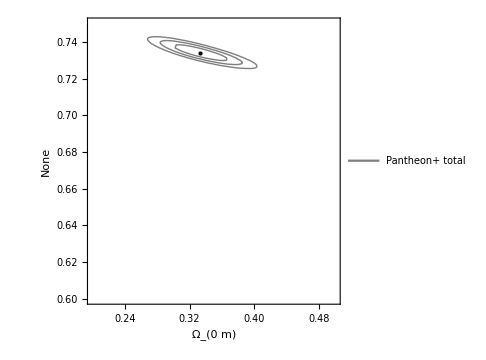

```mathematica
contour2 =ContourPlot[X2P[MP,om,-1,0,1,h],{om,0.2,0.5},{h,0.6,0.75},Contours->{minP[[1]]+dX[1,3],minP[[1]]+dX[2,3],minP[[1]]+dX[3,3]},Frame->{{False,True},{True,True}},FrameLabel->{"Ω_(0  m)","None"},BaseStyle->{FontFamily->"Times",25},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{omP,hP}]}},ContourShading->False,ContourStyle->Thick,ImageSize->Medium, WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"Pantheon+ total"},{0.6,0.6}]]
```

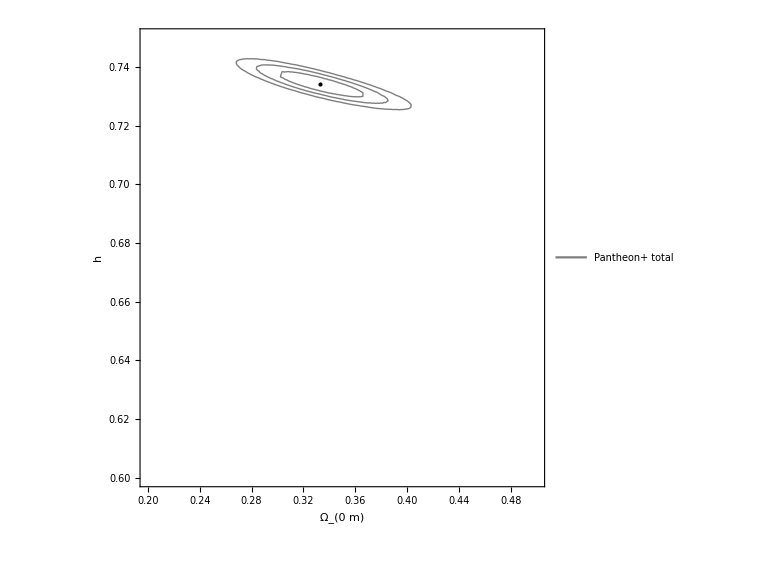

```mathematica
contour2frame =ContourPlot[X2P[MP,om,-1,0,1,h],{om,0.2,0.5},{h,0.6,0.75},Contours->{minP[[1]]+dX[1,3],minP[[1]]+dX[2,3],minP[[1]]+dX[3,3]},FrameLabel->{"Ω_(0  m)","h"},BaseStyle->{FontFamily->"Times",25},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{omP,hP}]}},ContourShading->False,ContourStyle->Thick,ImageSize->Large, WorkingPrecision->MachinePrecision,PlotLegends->Placed[{"Pantheon+ total"},{0.6,0.8}]]
```

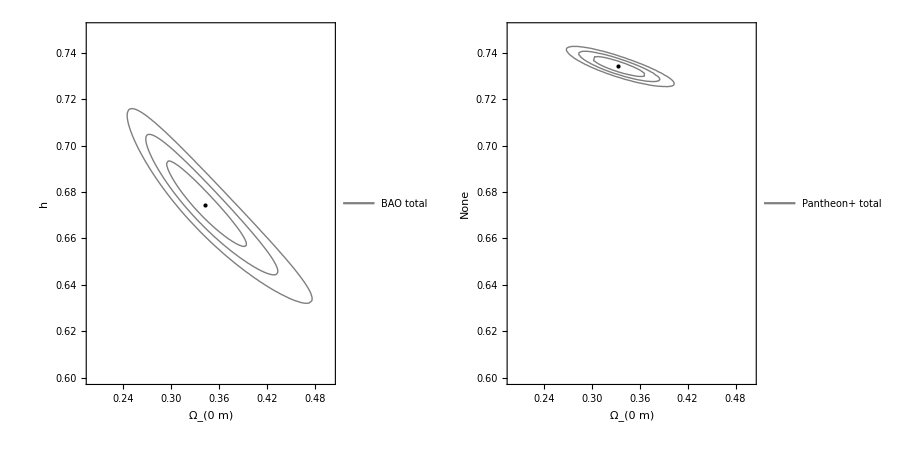

```mathematica
GraphicsGrid[{{contourBAOnew,contour2}},Spacings->-70,ImageSize->900]
```

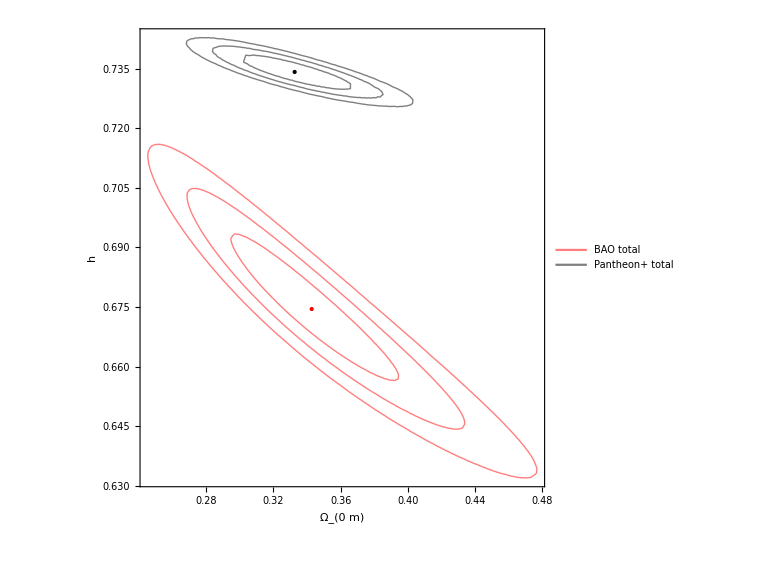

```mathematica
export=Show[contourBAOnewred,contour2frame,PlotRange->{All,All},Epilog->{{PointSize[Large],Black,Point[{omP,hP}]},{PointSize[Large],Red,Point[{omBaonew,hBaonew}]}}]
```